```mathematica
A={{1,0},{-1/2,Sqrt[3]/2},{-1/2,-Sqrt[3]/2}};
A={{1,0},{-1/2,Sqrt[3]/2},{-Sqrt[1-0.1^2],-0.1}};
```

```mathematica
mins[x_]:=Normalize[#-x]&/@A;
```

```mathematica
threeMins[x_]:=(Flatten[FirstPosition[#,Max[#]]&/@(mins[x].Transpose[A])]=={1,2,3});
```

```mathematica
newX[x_,grid_]:=With[{a=Max/@(grid.Transpose[A])},
Rest[LinearSolve[Prepend[#,1]&/@grid,a]]
];
```

```mathematica
pointRunsAway[x_]:=If[threeMins@NestWhile[newX[#,mins[#]]&,x,threeMins[x],1,10],0,1];
```

```mathematica
iterationsToZero[x_]:=With[{list=NestWhileList[newX[#,mins[#]]&,x,(Norm[#]>10^-9)&&(threeMins[#])&,1,15]},
If[Norm[Last[list]]<=10^-9,Length[list],15]];
```

```mathematica
sample=Table[{-j/100.,i/100.},{i,-100,100},{j,-100,100}]
```

{{{1.,-1.},{0.99,-1.},{0.98,-1.},{0.97,-1.},{0.96,-1.},{0.95,-1.},{0.94,-1.},{0.93,-1.},{0.92,-1.},{0.91,-1.},{0.9,-1.},{0.89,-1.},{0.88,-1.},{0.87,-1.},{0.86,-1.},{0.85,-1.},{0.84,-1.},{0.83,-1.},165,{-0.83,-1.},{-0.84,-1.},{-0.85,-1.},{-0.86,-1.},{-0.87,-1.},{-0.88,-1.},{-0.89,-1.},{-0.9,-1.},{-0.91,-1.},{-0.92,-1.},{-0.93,-1.},{-0.94,-1.},{-0.95,-1.},{-0.96,-1.},{-0.97,-1.},{-0.98,-1.},{-0.99,-1.},{-1.,-1.}},199,{1}}
 |  |  |  |

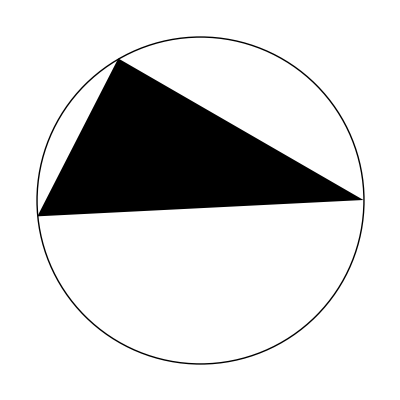

```mathematica
Graphics[{Circle[],Triangle[A]}]
```

```mathematica
ArrayPlot[Map[If[threeMins[#],1,0]&,sample,{2}]]
```

-Graphics-

```mathematica
ArrayPlot[Map[pointRunsAway[#]&,sample,{2}]]
```

-Graphics-

```mathematica
ArrayPlot[Map[iterationsToZero[#]&,sample,{2}],PlotLegends->Automatic,ImageSize->Large]
```

-Graphics-